```mathematica
Lx=100
Ly=100;
A=Lx*Ly;
```

100

```mathematica
m0 = 0.5;
```

```mathematica
LineChernListP1 = Import["dataPTB/dataPTBlocalChernSitesOnLineLx=100Ly=100m0=1.Xup=22Xdn=12PartsPerThousand=103Rational.dat"];
```

```mathematica
LineChernListP2 = Import["dataPTB/dataPTBlocalChernSitesOnLineLx=100Ly=100m0=-1.Xup=22Xdn=12PartsPerThousand=103Rational.dat"];
```

```mathematica
list1 = Table[LineChernListP1[[ii]][[3]],{ii,1,Lx}]
```

{-30.1807,0.985854,0.99612,0.998884,0.999504,0.999636,0.999691,0.999696,0.999667,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999668,0.999698,0.999698,0.999667,0.999691,0.999673,0.999489,0.998869,0.996164,0.986019,-30.1731}

```mathematica
list2 = Table[LineChernListP2[[ii]][[3]],{ii,1,Lx}]
```

{30.1807,-0.985854,-0.99612,-0.998884,-0.999504,-0.999636,-0.999691,-0.999696,-0.999667,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999668,-0.999698,-0.999698,-0.999667,-0.999691,-0.999673,-0.999489,-0.998869,-0.996164,-0.986019,30.1731}

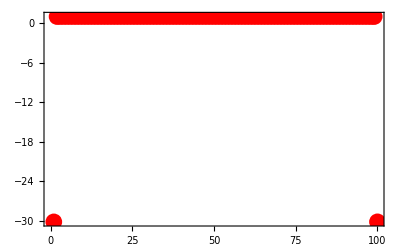

```mathematica
ListPlot[list1,PlotRange->All,Frame->True,PlotStyle-> {Red,PointSize[0.03]},Axes->False]
```

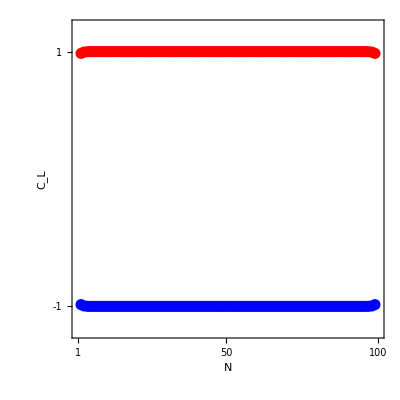

```mathematica
Show[(**Plot[1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,Axes->False],
Plot[-1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,Axes->False],**)
ListPlot[list1,PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,PlotStyle-> {Red,PointSize[0.02]},Axes->False],
ListPlot[list2,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Blue,PointSize[0.02]},Axes->False],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 24,
FrameTicks->{ {{{-1,"-1"},{1,"1"}},None},{{1,Lx/2,Lx},None}},
ImageSize-> 400,AspectRatio-> 1,
FrameLabel->{"N","C_L"},RotateLabel->False]
```